```mathematica
Exit
```

```mathematica
PacletDirectoryLoad["BHPT/SpinWeightedSpheroidalHarmonics"]
```

{/home/viktor/BHPT/SpinWeightedSpheroidalHarmonics}

```mathematica
<<Teukolsky`
```

```mathematica
Get["Documents/KerrSpinningFluxes/SpinningTrajectory.wl"]
Get["Documents/KerrSpinningFluxes/TeukolskySpinFluxes.wl"]
```

Orbital parameters

```mathematica
a=0.95`48
p=10.0`48
e=0.2`48
x=0.8`48
```

0.95

10.

0.2

0.8

Numerically calculated correction to the orbit

```mathematica
orbitCorrGenNum=KerrSpinOrbitCorrection[a, p, e, x, 8, 8]
```

Calculating t, ϕ equations

Calculating r equation

Calculating θ equation

Calculating norm equation

Calculating submatrices

Calculating v

Calculating ES,LS

Calculating UtSlist, UϕSlist

Calculating Uthatlist, Uϕhatlist

Calculating UtSfour, UϕSfour

Calculating Uthatfour, Uϕhatfour

Calculating ImΔtSfour, ImΔϕSfour

<|a→0.95,p→10.,e→0.2,ℐ→0.64350110879328438680280922871732263804151059112,Ehat→0.9544746770348815028245737919294451657838972805,Lzhat→2.79948425680011891564236595392544962217500193,Khat→8.0197239367489946559142268066245112912793203,TrajectoryCorrection→{Function[{SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$},SpinningOrbit`Private`ΔtS$11257[SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$]],Function[{SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$},SpinningOrbit`Private`rS$11257[SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$]],Function[{SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$},SpinningOrbit`Private`zS$11257[SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$]],Function[{SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$},SpinningOrbit`Private`ΔϕS$11257[SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$]]},TrajectoryGeo→{Function[{qt$,qr$,qθ$},qt$+37.66072847086401572836785676378822407973456 (0.999413390411955398085512051676789953825169 (π/2+qθ$)-EllipticE[JacobiAmplitude[1.0005871263100361282233286778813341185737146 (π/2+qθ$),0.0023454059187486273529280769211641734494410904],0.0023454059187486273529280769211641734494410904])-0.33817361288513973186269357261612270765611991 (-44.948693400468249365643857431842061032604956 (-8.715797818536671656955276473503844727558 (0.5059439843226725349628859729866393707486 qr$-EllipticPi[0.0001841712845929680574511269209054036693793,JacobiAmplitude[0.505897118062944032352131957184415457949557 qr$,0.04594999780221134188374541608125003015055563],0.04594999780221134188374541608125003015055563])+0.2020991546530951596132878618750486375788946 (0.5138663607127461504485150319017451954413448 qr$-EllipticPi[0.03059916228279354923394371188192864618810053,JacobiAmplitude[0.505897118062944032352131957184415457949557 qr$,0.04594999780221134188374541608125003015055563],0.04594999780221134188374541608125003015055563]))+185.8084378216365257371440228116034607695374 (0.639534709428175376839293227058901935148601 qr$-EllipticPi[0.3725467329299748343441276990258976572072919,JacobiAmplitude[0.505897118062944032352131957184415457949557 qr$,0.04594999780221134188374541608125003015055563],0.04594999780221134188374541608125003015055563])+89.529529757449739111338408326286046756355518 (0.4942057923127259889166562805682094528702252 qr$-EllipticE[JacobiAmplitude[0.505897118062944032352131957184415457949557 qr$,0.04594999780221134188374541608125003015055563],0.04594999780221134188374541608125003015055563]+(0.3725467329299748343441276990258976572072919 JacobiCN[0.505897118062944032352131957184415457949557 qr$,0.04594999780221134188374541608125003015055563] JacobiSN[0.505897118062944032352131957184415457949557 qr$,0.04594999780221134188374541608125003015055563] √(1-0.04594999780221134188374541608125003015055563 JacobiSN[0.505897118062944032352131957184415457949557 qr$,0.04594999780221134188374541608125003015055563]^2))/(1-0.3725467329299748343441276990258976572072919 JacobiSN[0.505897118062944032352131957184415457949557 qr$,0.04594999780221134188374541608125003015055563]^2))),Listable],Function[{qr$},(-93.202326454836286463247075469243991457090653+5.482170105915190101709795598711337604788007 JacobiSN[0.505897118062944032352131957184415457949557 qr$,0.04594999780221134188374541608125003015055563]^2)/(-11.184279174580354375589649056309278974850878+4.1666666666666666666666666666666666666666666667 JacobiSN[0.505897118062944032352131957184415457949557 qr$,0.04594999780221134188374541608125003015055563]^2),Listable],Function[{qθ$},ArcCos[0.6 JacobiSN[1.0005871263100361282233286778813341185737146 (π/2+qθ$),0.0023454059187486273529280769211641734494410904]],Listable],Function[{qϕ$,qr$,qθ$},qϕ$+1.0288712096409793695217593013980787298979828 (-46.61009445803144762574408165284621114352 (0.5059439843226725349628859729866393707486 qr$-EllipticPi[0.0001841712845929680574511269209054036693793,JacobiAmplitude[0.505897118062944032352131957184415457949557 qr$,0.04594999780221134188374541608125003015055563],0.04594999780221134188374541608125003015055563])+2.062164084552230624278761438206890087165815 (0.5138663607127461504485150319017451954413448 qr$-EllipticPi[0.03059916228279354923394371188192864618810053,JacobiAmplitude[0.505897118062944032352131957184415457949557 qr$,0.04594999780221134188374541608125003015055563],0.04594999780221134188374541608125003015055563]))-0.79738973499649480880213907443707012421368236 (1.2508154931005795747794382586319016068093013 (π/2+qθ$)-EllipticPi[0.36,JacobiAmplitude[1.0005871263100361282233286778813341185737146 (π/2+qθ$),0.0023454059187486273529280769211641734494410904],0.0023454059187486273529280769211641734494410904]),Listable]},MinoFrequenciesGeo→{124.7629736005981287023759422670878097996,2.78953935181040098671000383825122170656255,3.5087504235493092486810623834629999915272225,3.69314850594018026158987829353258678045},BLFrequenciesGeo→{0.02235871165383178715389082048398869326539,0.02812333116379399823078257715580813748831,0.0296013183988624880244706636949406850169},FourVelocityCorrection→{Function[{SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$},SpinningOrbit`Private`udtS$11257[SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$]],Function[{SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$},(10. 0.2 (SpinningOrbit`Private`χrhat$11257'[SpinningOrbit`Private`wr$] (Cos[SpinningOrbit`Private`χrhat$11257[SpinningOrbit`Private`wr$]] SpinningOrbit`Private`δχrS$11257[SpinningOrbit`Private`wr$] SpinningOrbit`Private`Υrhat$11257+Sin[SpinningOrbit`Private`χrhat$11257[SpinningOrbit`Private`wr$]] SpinningOrbit`Private`ΥrS$11257+(2 0.2 Sin[SpinningOrbit`Private`χrhat$11257[SpinningOrbit`Private`wr$]]^2 SpinningOrbit`Private`δχrS$11257[SpinningOrbit`Private`wr$] SpinningOrbit`Private`Υrhat$11257)/(1+0.2 Cos[SpinningOrbit`Private`χrhat$11257[SpinningOrbit`Private`wr$]]))+Sin[SpinningOrbit`Private`χrhat$11257[SpinningOrbit`Private`wr$]] SpinningOrbit`Private`dδχrS$11257[SpinningOrbit`Private`wr$]))/(1+0.2 Cos[SpinningOrbit`Private`χrhat$11257[SpinningOrbit`Private`wr$]])^2+SpinningOrbit`Private`dδ𝔯$11257[SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$]],Function[{SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$},-Sin[SpinningOrbit`Private`ℐ$11257] (SpinningOrbit`Private`χθhat$11257'[SpinningOrbit`Private`wz$] (Cos[SpinningOrbit`Private`χθhat$11257[SpinningOrbit`Private`wz$]] SpinningOrbit`Private`δχθS$11257[SpinningOrbit`Private`wz$] SpinningOrbit`Private`Υθhat$11257+Sin[SpinningOrbit`Private`χθhat$11257[SpinningOrbit`Private`wz$]] SpinningOrbit`Private`ΥθS$11257)+Sin[SpinningOrbit`Private`χθhat$11257[SpinningOrbit`Private`wz$]] SpinningOrbit`Private`dδχθS$11257[SpinningOrbit`Private`wz$])+SpinningOrbit`Private`dδ𝔷$11257[SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$]],Function[{SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$},SpinningOrbit`Private`udϕS$11257[SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$]]},Spin4vector→{Function[{SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$},SpinningOrbit`Private`St$11257[SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$]],Function[{SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$},SpinningOrbit`Private`Sr$11257[SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$]],Function[{SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$},SpinningOrbit`Private`Sz$11257[SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$]],Function[{SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$},SpinningOrbit`Private`Sϕ$11257[SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$]]},TrajectoryDeltas→<|Δtr→Function[{qr$},-0.33817361288513973186269357261612270765611991 (-44.948693400468249365643857431842061032604956 (-8.715797818536671656955276473503844727558 (0.5059439843226725349628859729866393707486 qr$-EllipticPi[0.0001841712845929680574511269209054036693793,JacobiAmplitude[0.505897118062944032352131957184415457949557 qr$,0.04594999780221134188374541608125003015055563],0.04594999780221134188374541608125003015055563])+0.2020991546530951596132878618750486375788946 (0.5138663607127461504485150319017451954413448 qr$-EllipticPi[0.03059916228279354923394371188192864618810053,JacobiAmplitude[0.505897118062944032352131957184415457949557 qr$,0.04594999780221134188374541608125003015055563],0.04594999780221134188374541608125003015055563]))+185.8084378216365257371440228116034607695374 (0.639534709428175376839293227058901935148601 qr$-EllipticPi[0.3725467329299748343441276990258976572072919,JacobiAmplitude[0.505897118062944032352131957184415457949557 qr$,0.04594999780221134188374541608125003015055563],0.04594999780221134188374541608125003015055563])+89.529529757449739111338408326286046756355518 (0.4942057923127259889166562805682094528702252 qr$-EllipticE[JacobiAmplitude[0.505897118062944032352131957184415457949557 qr$,0.04594999780221134188374541608125003015055563],0.04594999780221134188374541608125003015055563]+(0.3725467329299748343441276990258976572072919 JacobiCN[0.505897118062944032352131957184415457949557 qr$,0.04594999780221134188374541608125003015055563] JacobiSN[0.505897118062944032352131957184415457949557 qr$,0.04594999780221134188374541608125003015055563] √(1-0.04594999780221134188374541608125003015055563 JacobiSN[0.505897118062944032352131957184415457949557 qr$,0.04594999780221134188374541608125003015055563]^2))/(1-0.3725467329299748343441276990258976572072919 JacobiSN[0.505897118062944032352131957184415457949557 qr$,0.04594999780221134188374541608125003015055563]^2))),Listable],Δtθ→Function[{qθ$},37.66072847086401572836785676378822407973456 (0.999413390411955398085512051676789953825169 (π/2+qθ$)-EllipticE[JacobiAmplitude[1.0005871263100361282233286778813341185737146 (π/2+qθ$),0.0023454059187486273529280769211641734494410904],0.0023454059187486273529280769211641734494410904]),Listable],Δϕr→Function[{qr$},1.0288712096409793695217593013980787298979828 (-46.61009445803144762574408165284621114352 (0.5059439843226725349628859729866393707486 qr$-EllipticPi[0.0001841712845929680574511269209054036693793,JacobiAmplitude[0.505897118062944032352131957184415457949557 qr$,0.04594999780221134188374541608125003015055563],0.04594999780221134188374541608125003015055563])+2.062164084552230624278761438206890087165815 (0.5138663607127461504485150319017451954413448 qr$-EllipticPi[0.03059916228279354923394371188192864618810053,JacobiAmplitude[0.505897118062944032352131957184415457949557 qr$,0.04594999780221134188374541608125003015055563],0.04594999780221134188374541608125003015055563])),Listable],Δϕθ→Function[{qθ$},-0.79738973499649480880213907443707012421368236 (1.2508154931005795747794382586319016068093013 (π/2+qθ$)-EllipticPi[0.36,JacobiAmplitude[1.0005871263100361282233286778813341185737146 (π/2+qθ$),0.0023454059187486273529280769211641734494410904],0.0023454059187486273529280769211641734494410904]),Listable]|>,MinoFrequenciesCorrection→{-0.304381976349456,0.1533933022367093,-0.06343492075054213,-0.1565255075503621},BLFrequenciesCorrection→{0.001284025912939304,-0.0004398314984463723,-0.001182365212180704},ES→-0.00146215379788602,LS→0.5074309528696018,δχrS→SpinningOrbit`Private`δχrS$11257,δχθS→SpinningOrbit`Private`δχθS$11257,δr→SpinningOrbit`Private`δ𝔯$11257,δz→SpinningOrbit`Private`δ𝔷$11257,OrbitCorrection→Function[{SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$},SpinningOrbit`Private`OrbitCorrection$11257[SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$]],error→5.510458×10^-8|>

```mathematica
lists=2^Range[0,4]/16*0.2`48
```

{0.0125,0.025,0.05,0.1,0.2}

Analytically calculated orbits for different spins

```mathematica
orbitsGenAna=Table[KerrSpinOrbit[a,p,e,x,s,"Gauge"->"pex"],{s,lists}];
```

Mode numbers

```mathematica
l=3
m=2
n=1
k=1
```

3

2

1

1

Modes from numerical trajectory

```mathematica
modesGenNum=Table[TeukolskySpinModeFromCorrection[l,m,n,k,orbitCorrGenNum,s],{s,lists}]
```

128 steps in wr, 64 steps in wθ

128 steps in wr, 64 steps in wθ

128 steps in wr, 64 steps in wθ

«2 more identical outputs»

{<|l→3,m→2,k→1,n→1,ω→0.1096656729152274055,Amplitudes→<|ℐ→0.0001189976977522+0.0002191454103096 ⅈ,ℋ→0.000017290720974882-0.000062239933676598 ⅈ|>,α→-0.000350345554862855567,S→-0.371864110314551,Fluxes→<|Energy→<|ℐ→4.114674611344×10^-7,ℋ→-9.6732107769567×10^-12|>,AngularMomentum→<|ℐ→7.504033854832×10^-6,ℋ→-1.7641273736467×10^-10|>,CarterConstantK→<|ℐ→0.00006386900585759,ℋ→-1.5014999097907×10^-9|>|>,stepsr→128,stepsθ→64|>,<|l→3,m→2,k→1,n→1,ω→0.1096466662151040495,Amplitudes→<|ℐ→0.0001188298822693+0.000218859497935 ⅈ,ℋ→0.00001728810816639-0.000062228771238264 ⅈ|>,α→-0.000350205476171110287,S→-0.371864378145466,Fluxes→<|Energy→<|ℐ→4.1051703175×10^-7,ℋ→-9.669265626079×10^-12|>,AngularMomentum→<|ℐ→7.487998421123×10^-6,ℋ→-1.763713564644×10^-10|>,CarterConstantK→<|ℐ→0.000063965086508,ℋ→-1.506625461078×10^-9|>|>,stepsr→128,stepsθ→64|>,<|l→3,m→2,k→1,n→1,ω→0.109608652814857338,Amplitudes→<|ℐ→0.0001184945943658+0.0002182880860137 ⅈ,ℋ→0.00001728285175211-0.00006220616566874 ⅈ|>,α→-0.00034992538809447984,S→-0.37186491376513,Fluxes→<|Energy→<|ℐ→4.086202209855×10^-7,ℋ→-9.661293938375×10^-12|>,AngularMomentum→<|ℐ→7.455984732805×10^-6,ℋ→-1.762870665821×10^-10|>,CarterConstantK→<|ℐ→0.00006415361162815,ℋ→-1.516828750308×10^-9|>|>,stepsr→128,stepsθ→64|>,<|l→3,m→2,k→1,n→1,ω→0.109532626014363914,Amplitudes→<|ℐ→0.000117825431951+0.0002171469205608 ⅈ,ℋ→0.00001727221486589-0.00006215983143716 ⅈ|>,α→-0.00034936548934269633,S→-0.3718659848358,Fluxes→<|Energy→<|ℐ→4.04842855178×10^-7,ℋ→-9.645025411522×10^-12|>,AngularMomentum→<|ℐ→7.39218751361×10^-6,ℋ→-1.761123742301×10^-10|>,CarterConstantK→<|ℐ→0.0000645163478112,ℋ→-1.53704531558×10^-9|>|>,stepsr→128,stepsθ→64|>,<|l→3,m→2,k→1,n→1,ω→0.109380572413377066,Amplitudes→<|ℐ→0.000116492694884+0.000214871228612 ⅈ,ℋ→0.0000172504376843-0.00006206266783484 ⅈ|>,α→-0.00034824680283594764,S→-0.37186812630249,Fluxes→<|Energy→<|ℐ→3.97352886826×10^-7,ℋ→-9.61119092445×10^-12|>,AngularMomentum→<|ℐ→7.26551119745×10^-6,ℋ→-1.75738537702×10^-10|>,CarterConstantK→<|ℐ→0.0000651862219371,ℋ→-1.57672750206×10^-9|>|>,stepsr→128,stepsθ→64|>}

Modes from analytical trajectory

```mathematica
modesGenAna=Table[TeukolskySpinModeAnalytical[l,m,n,k,orbitsGenAna[[i]]],{i,1,Length[lists]}]
```

128 steps in wr, 64 steps in wz

128 steps in wr, 64 steps in wz

128 steps in wr, 64 steps in wz

«2 more identical outputs»

{<|l→3,m→2,k→1,n→1,ω→0.1096678058625859758929940057620040641,Amplitudes→<|ℐ→0.0001189940500497264604917940889323+0.0002191201729290357754981526097931 ⅈ,ℋ→0.00001728893360968772471731681496427-0.000062239346735021320567211777184991 ⅈ|>,α→-0.000350361276049007482699121659994764162,S→-0.371864080257470701726866114021484,Fluxes→<|Energy→<|ℐ→4.113725283595914527413021944297×10^-7,ℋ→-9.6729559114473105199290857079617×10^-12|>,AngularMomentum→<|ℐ→7.502156628811234149506065059279×10^-6,ℋ→-1.7640465832912801239121282195109×10^-10|>,CarterConstantK→<|ℐ→0.0000638531736030910900276176442621,ℋ→-1.501434564752433558475897423881×10^-9|>|>,stepsr→128,stepsθ→64|>,<|l→3,m→2,k→1,n→1,ω→0.1096551960345402803198780429208600276,Amplitudes→<|ℐ→0.0001188149267357233151103672414859+0.0002187565825218856436877953455136 ⅈ,ℋ→0.00001728102990871822927290608120854-0.000062226516770165050689861709054982 ⅈ|>,α→-0.000350268337774668127136195978242289943,S→-0.371864257950151140989214346209403,Fluxes→<|Energy→<|ℐ→4.101315854265218146646628030606×10^-7,ℋ→-9.668279112275533942712400319146×10^-12|>,AngularMomentum→<|ℐ→7.480385795805508450701865053766×10^-6,ℋ→-1.763396439368021115236543210393×10^-10|>,CarterConstantK→<|ℐ→0.00006390063321519786019792234662677,ℋ→-1.506368149463979443201978032194×10^-9|>|>,stepsr→128,stepsθ→64|>,<|l→3,m→2,k→1,n→1,ω→0.109642760313945997681446869254474356,Amplitudes→<|ℐ→0.0001184316238690746095517140745215+0.0002178604437651092787947200910935 ⅈ,ℋ→0.00001725508964064927274796862885221-0.00006219787847092119616162529240264 ⅈ|>,α→-0.00035017669268212174488027997665808867,S→-0.37186443318331973522842038417003,Fluxes→<|Energy→<|ℐ→4.07032620887301731667149839131×10^-7,ℋ→-9.657605715885539722132242036252×10^-12|>,AngularMomentum→<|ℐ→7.42470583049575534114659481475×10^-6,ℋ→-1.761649503940323860536472254458×10^-10|>,CarterConstantK→<|ℐ→0.0000638867402476844964875673614733,ℋ→-1.515831695357321648558767096842×10^-9|>|>,stepsr→128,stepsθ→64|>,<|l→3,m→2,k→1,n→1,ω→0.109669025429742906512983857347407007,Amplitudes→<|ℐ→0.000117546863262089480833372508504+0.0002152995653315935589175412330069 ⅈ,ℋ→0.00001716528526747699972647560610343-0.00006213229629015105134027729232036 ⅈ|>,α→-0.00035037026516960760380582128479769158,S→-0.37186406307148739200829515881965,Fluxes→<|Energy→<|ℐ→3.98116895428825980131932180936×10^-7,ℋ→-9.632248469610854880641689855845×10^-12|>,AngularMomentum→<|ℐ→7.26033433540213182995051918868×10^-6,ℋ→-1.75660327642494587703088579897×10^-10|>,CarterConstantK→<|ℐ→0.000063374225038910040802014869105,ℋ→-1.533309159075734170060574343586×10^-9|>|>,stepsr→128,stepsθ→64|>,<|l→3,m→2,k→1,n→1,ω→0.109926946244914082490667107677829068,Amplitudes→<|ℐ→0.000115141894863135872404954962345+0.000206215341071395330024107734941 ⅈ,ℋ→0.0000168513905110402310742313260248-0.00006199420013006205026952989537937 ⅈ|>,α→-0.00035227346784622409649266942154716438,S→-0.37186042718435533875069660141879,Fluxes→<|Energy→<|ℐ→3.67349271066279312100192778195×10^-7,ℋ→-9.574641949034026847553462574728×10^-12|>,AngularMomentum→<|ℐ→6.68351634635307116075022634025×10^-6,ℋ→-1.742000897159828178299895497387×10^-10|>,CarterConstantK→<|ℐ→0.0000599949327247697366252852062319,ℋ→-1.563716181955925529053152212692×10^-9|>|>,stepsr→128,stepsθ→64|>}

Difference between modes is O(s^2)

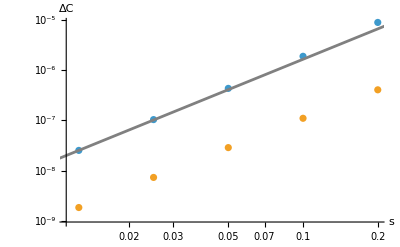

```mathematica
Show[ListLogLogPlot[{Table[{lists[[i]],Abs[modesGenNum[[i]]["Amplitudes"]["ℐ"]-modesGenAna[[i]]["Amplitudes"]["ℐ"]]},{i,1,Length[lists]}],Table[{lists[[i]],Abs[modesGenNum[[i]]["Amplitudes"]["ℋ"]-modesGenAna[[i]]["Amplitudes"]["ℋ"]]},{i,1,Length[lists]}]},AxesLabel->{s,ΔC}],LogLogPlot[(s/0.0125)^2*2.55*^-8,{s,0.001,1},PlotStyle->Gray]]
```

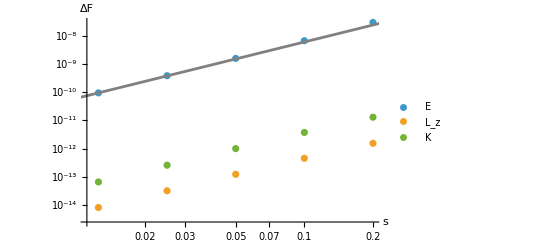

```mathematica
Show[ListLogLogPlot[{Table[{lists[[i]],Abs[modesGenNum[[i]]["Fluxes"]["Energy"]["ℐ"]-modesGenAna[[i]]["Fluxes"]["Energy"]["ℐ"]]},{i,1,Length[lists]}],
Table[{lists[[i]],Abs[modesGenNum[[i]]["Fluxes"]["AngularMomentum"]["ℋ"]-modesGenAna[[i]]["Fluxes"]["AngularMomentum"]["ℋ"]]},{i,1,Length[lists]}],
Table[{lists[[i]],Abs[modesGenNum[[i]]["Fluxes"]["CarterConstantK"]["ℋ"]-modesGenAna[[i]]["Fluxes"]["CarterConstantK"]["ℋ"]]},{i,1,Length[lists]}]},AxesLabel->{s,ΔF},PlotLegends->{"E", "L_z","K"}],LogLogPlot[(s/0.0125)^2*9.49*^-11,{s,0.001,1},PlotStyle->Gray]]
```